```mathematica
(******************************** Input data ***********************************)
(* μ and ω sets *)
ω=Table[10^i,{i,-4,4}];
logo=Table[N[Log[10^i]],{i,-4,4}];
m={1,1.5,2,3,10,50,207,400,900,1836};
μ=Table[N[m[[i]]/(1+m[[i]])],{i,1,10}];

(* mu-excluded a parameters for each μ *)
a[1]={1.000000,0.999994,0.999407,0.969414,0.876121,0.829982,0.814620,0.809723,0.808173};
a[2]={1.000000,0.999996,0.999587,0.975533,0.882113,0.832107,0.815302,0.809940,0.808241};
a[3]={1.000000,0.999997,0.999665,0.978707,0.885764,0.833423,0.815726,0.810074,0.808284};
a[4]={1.000000,0.999997,0.999735,0.981924,0.890005,0.834976,0.816227,0.810234,0.808335};
a[5]={1.000000,0.999998,0.999819,0.986419,0.897291,0.837710,0.817110,0.810515,0.808423};
a[6]={1.000000,0.999998,0.999844,0.987933,0.900267,0.838853,0.817480,0.810632,0.808460};
a[7]={1.000000,0.999998,0.999850,0.988260,0.900959,0.839085,0.817555,0.810655,0.808469};
a[8]={1.000000,0.999998,0.999850,0.988260,0.900959,0.839121,0.817567,0.810659,0.808469};
a[9]={1.000000,0.999998,0.999850,0.988286,0.901014,0.839143,0.817574,0.810661,0.808469};
a[10]={1.000000,0.999998,0.999850,0.988296,0.901037,0.839152,0.817577,0.810662,0.808470};

(* mu-excluded b parameters for each μ *)
b[1]={0.000000,0.000003,0.000298,0.021117,0.410215,4.732543,49.173238,497.405074,4991.813767};
b[2]={0.000000,0.000003,0.000249,0.018938,0.400996,4.706122,49.093389,497.156451,4991.031476};
b[3]={0.000000,0.000002,0.000224,0.017692,0.395239,4.689644,49.043735,497.002015,4990.545724};
b[4]={0.000000,0.000002,0.000199,0.016325,0.388406,4.670093,48.984959,496.819371,4989.971417};
b[5]={0.000000,0.000002,0.000165,0.014179,0.376287,4.635388,48.880985,496.496718,4988.957410};
b[6]={0.000000,0.000002,0.000153,0.013376,0.371188,4.620756,48.837283,496.361283,4988.531880};
b[7]={0.000000,0.000002,0.000150,0.013195,0.369991,4.617781,48.828408,496.333788,4988.432061};
b[8]={0.000000,0.000002,0.000150,0.013195,0.369991,4.617317,48.827026,496.329506,4988.432061};
b[9]={0.000000,0.000002,0.000150,0.013180,0.369894,4.617041,48.826200,496.326955,4988.424026};
b[10]={0.000000,0.000002,0.000150,0.013175,0.369855,4.616927,48.825863,496.325903,4988.420744};



(* double sets of {Logo,exp}*)
setEXa=Table[{logo[[j]],a[i][[j]]},{i,10},{j,9}];
dataEXa=FlattenAt[setEXa,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];

setEXb=Table[{logo[[j]],b[i][[j]]},{i,10},{j,9}];
dataEXb=FlattenAt[setEXb,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];

(* data matrix containing corresponding a, b, μ, ω *)
datamat=Table[{a[i][[j]],b[i][[j]],μ[[i]],ω[[j]]},{i,10},{j,9}];
```

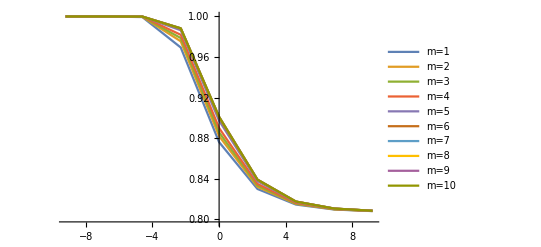

```mathematica
(******************************** Plotting ***********************************)
(* plotting mu-excluded a and b parameters for each mass versus different omega *)
ListLinePlot[Table[setEXa[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

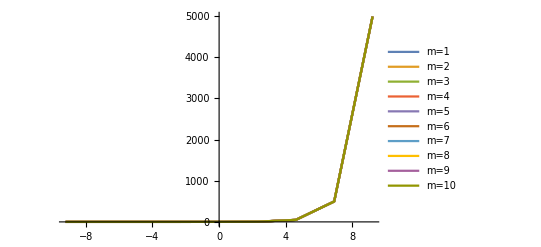

```mathematica
ListLinePlot[Table[setEXb[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

FittedModel[0.812381+0.18979/(1+ⅇ^(0.919844 («20»+x)))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.18979 | 0.00159792 | 118.773 | 3.79227×10^-97
bb | -0.919844 | 0.034131 | -26.9504 | 1.05244×10^-43
c | -0.206794 | 0.0423064 | -4.88801 | 4.68063×10^-6
d | 0.812381 | 0.00103838 | 782.356 | 1.91202×10^-167

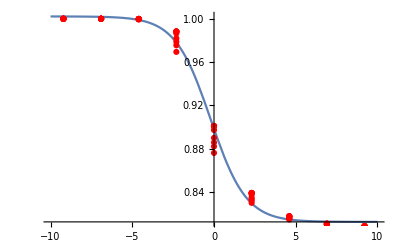

```mathematica
(******************************** Fitting ***********************************)
(* fitting all data to Logistic function *)
fitA=NonlinearModelFit[dataEXa,{aa/(1+Exp[-bb *(x-c)])+d},{aa,bb,c,d},x,Method->"NMinimize"]
fitA["ParameterTable"]
Show[{Plot[fitA[x],{x,-10,10}],ListPlot[dataEXa,PlotStyle->Red]}]
```

FittedModel[0.811694+0.190257/(1+ⅇ^(0.914937 («17»+x)))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.190257 | 0.00372168 | 51.1214 | 5.41394×10^-8
bb | -0.914937 | 0.0737289 | -12.4095 | 0.000060226
c | -0.652104 | 0.102432 | -6.36624 | 0.00141393
d | 0.811694 | 0.00234306 | 346.424 | 3.80385×10^-12

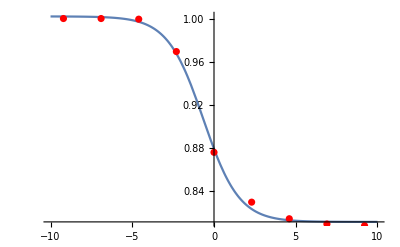

```mathematica
(* fit for selected masses: 1, 10, 1836 *)
fit1=NonlinearModelFit[setEXa[[1]],{aa/(1+Exp[-bb *(x-c)])+d},{aa,bb,c,d},x,Method->"NMinimize"]
fit1["ParameterTable"]
Show[{Plot[fit1[x],{x,-10,10}],ListPlot[setEXa[[1]],PlotStyle->Red]}]
```

FittedModel[0.812542+0.189761/(1+ⅇ^(0.926165 («20»+x)))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.189761 | 0.00498991 | 38.029 | 2.36875×10^-7
bb | -0.926165 | 0.108765 | -8.5153 | 0.000367436
c | -0.115103 | 0.13105 | -0.878309 | 0.419973
d | 0.812542 | 0.00327181 | 248.347 | 2.00881×10^-11

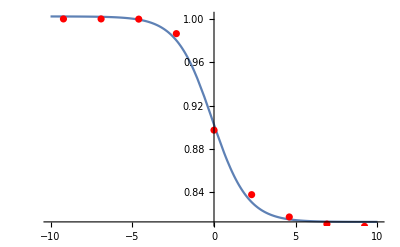

```mathematica
fit5=NonlinearModelFit[setEXa[[5]],{aa/(1+Exp[-bb *(x-c)])+d},{aa,bb,c,d},x,Method->"NMinimize"]
fit5["ParameterTable"]
Show[{Plot[fit5[x],{x,-10,10}],ListPlot[setEXa[[5]],PlotStyle->Red]}]
```

FittedModel[0.812512+0.189915/(1+ⅇ^(0.915913 («20»+x)))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.189915 | 0.00511525 | 37.1273 | 2.66973×10^-7
bb | -0.915913 | 0.109275 | -8.38172 | 0.000395899
c | -0.0263528 | 0.134711 | -0.195625 | 0.852606
d | 0.812512 | 0.00338381 | 240.117 | 2.37743×10^-11

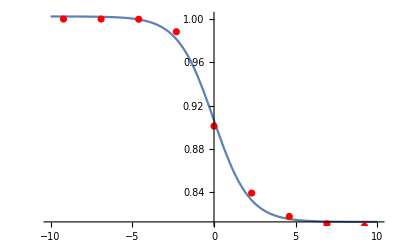

```mathematica
fit10=NonlinearModelFit[setEXa[[10]],{aa/(1+Exp[-bb *(x-c)])+d},{aa,bb,c,d},x,Method->"NMinimize"]
fit10["ParameterTable"]
Show[{Plot[fit10[x],{x,-10,10}],ListPlot[setEXa[[10]],PlotStyle->Red]}]
```

FittedModel[0.905376-0.0946643 Erf[0.37044 x]]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.905376 | 0.000657208 | 1377.61 | 1.56738×10^-190
bb | 0.0946643 | 0.000863482 | 109.631 | 4.91035×10^-95
cc | 0.37044 | 0.0133838 | 27.6783 | 6.67755×10^-45

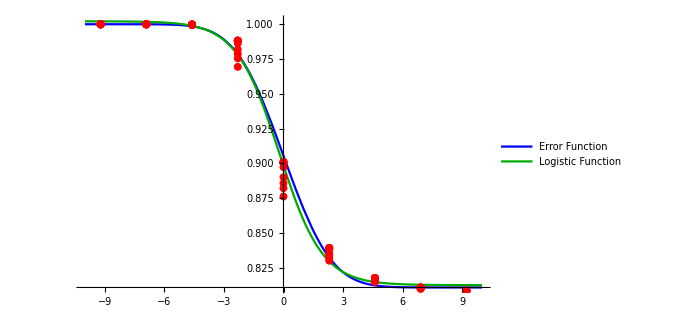

```mathematica
(* comparision of fitting quality for logistic function vs error function *)
fitA2=NonlinearModelFit[dataEXa,{aa-bb*Erf[x*cc]},{aa,bb,cc},x,Method->"NMinimize"]
fitA2["ParameterTable"]
Show[{Plot[{fitA2[x],fitA[x]},{x,-10,10},PlotStyle->{Blue,Darker[Green]},PlotLegends->{"Error Function","Logistic Function"}],ListPlot[dataEXa,PlotStyle->Red]}]
```

FittedModel[0.893518 ⅇ^(1.00209 (-0.600658+x))]

| Estimate | Standard Error | t-Statistic | P-Value
b1 | 0.893518 | 0.000553649 | 1613.87 | 1.63997×10^-196
b2 | 1.00209 | 0.000129968 | 7710.29 | 1.3331×10^-255
b3 | -0.600658 | 0.000495729 | -1211.66 | 1.10831×10^-185

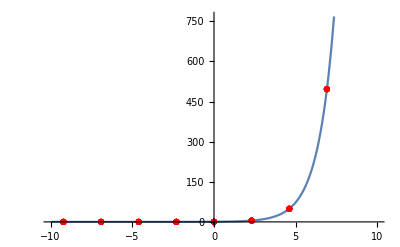

```mathematica
(* fitting all b data to Exponential function *)
fitB=NonlinearModelFit[dataEXb,{b1*Exp[b2 *(x+b3)]},{b1,b2,b3},x,Method->"NMinimize"]
fitB["ParameterTable"]
Show[{Plot[fitB[x],{x,-10,10}],ListPlot[dataEXb,PlotStyle->Red]}]
```

FittedModel[0.895792 ⅇ^(1.00161 (-0.598605+x))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.895792 | 0.000662292 | 1352.56 | 1.10244×10^-17
bb | 1.00161 | 0.000155326 | 6448.45 | 9.38797×10^-22
cc | -0.598605 | 0.000594231 | -1007.36 | 6.45932×10^-17

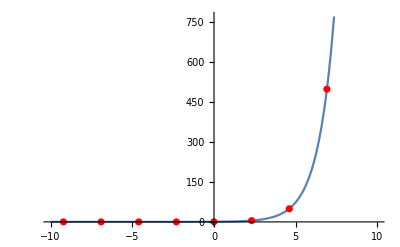

```mathematica
(* fit for each set of b *)
fit1b=NonlinearModelFit[setEXb[[1]],{aa*Exp[bb *(x+cc)]},{aa,bb,cc},x,Method->"NMinimize"]
fit1b["ParameterTable"]
Show[{Plot[fit1b[x],{x,-10,10}],ListPlot[setEXb[[1]],PlotStyle->Red]}]
```

FittedModel[0.893046 ⅇ^(1.00219 (-0.601084+x))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.893046 | 0.000901404 | 990.728 | 7.1379×10^-17
bb | 1.00219 | 0.000211644 | 4735.26 | 5.98741×10^-21
cc | -0.601084 | 0.000806758 | -745.061 | 3.94585×10^-16

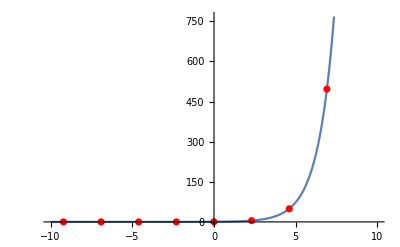

```mathematica
fit5b=NonlinearModelFit[setEXb[[5]],{aa*Exp[bb *(x+cc)]},{aa,bb,cc},x,Method->"NMinimize"]
fit5b["ParameterTable"]
Show[{Plot[fit5b[x],{x,-10,10}],ListPlot[setEXb[[5]],PlotStyle->Red]}]
```

FittedModel[0.892558 ⅇ^(1.00229 (-0.601525+x))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.892558 | 0.000946862 | 942.649 | 9.62048×10^-17
bb | 1.00229 | 0.000222362 | 4507.48 | 8.04821×10^-21
cc | -0.601525 | 0.000847065 | -710.128 | 5.26344×10^-16

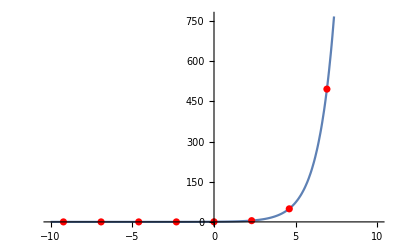

```mathematica
fit10b=NonlinearModelFit[setEXb[[10]],{aa*Exp[bb *(x+cc)]},{aa,bb,cc},x,Method->"NMinimize"]
fit10b["ParameterTable"]
Show[{Plot[fit10b[x],{x,-10,10}],ListPlot[setEXb[[10]],PlotStyle->Red]}]
```

FittedModel[-0.681392 ⅇ^(0.497864 (-3.70873+Log[x]))+x/2]

| Estimate | Standard Error | t-Statistic | P-Value
aa | -0.681392 | 0.0493448 | -13.8088 | 1.21636×10^-23
bb | 0.497864 | 0.0152197 | 32.7119 | 1.14933×10^-50
cc | -3.70873 | 0.0167398 | -221.552 | 1.62387×10^-121

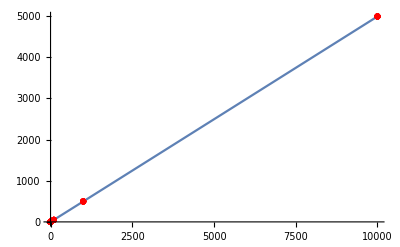

```mathematica
(* fitting b data to Exponential function *)
fitB2=NonlinearModelFit[setBo,{aa*Exp[bb *(Log[x]+cc)]+1/2 x},{aa,bb,cc},x,Method->"NMinimize"]
fitB2["ParameterTable"]
Show[{Plot[fitB2[x],{x,0,10^4}],ListPlot[setBo,PlotStyle->Red]}]
```

```mathematica
(* fitting all data to Exponential function *)
fitB=NonlinearModelFit[setBo,{b1*Exp[b2 *(Log[x]+b3)]+1/2 x},{b1,b2,b3},x,Method->"NMinimize"]
fitB["ParameterTable"]
Show[{Plot[fitB[x],{x,0,10000}],ListPlot[setBo,PlotStyle->Red]}]
```

FittedModel[-0.681392 ⅇ^(0.497864 (-3.70873+Log[x]))+x/2]

| Estimate | Standard Error | t-Statistic | P-Value
b1 | -0.681392 | 0.0493448 | -13.8088 | 1.21636×10^-23
b2 | 0.497864 | 0.0152197 | 32.7119 | 1.14933×10^-50
b3 | -3.70873 | 0.0167398 | -221.552 | 1.62387×10^-121

-Graphics-

```mathematica
(******************************** Percentage Errors ***********************************)

(* a parameters *)
(* logistic function *)
alog1=0.18;
alog2=-0.9;
alog3=-0.2;
alog4=0.81;
aparLOG[x_]:=alog1/(1+Exp[-alog2 *(x-alog3)])+alog4;
amatlog=Table[aparLOG[logo[[i]]],{i,9}];

(* Error function *)
aerr1=0.9;
aerr2=0.09;
aerr3=0.37;
aparERR[x_]:=aerr1-aerr2*Erf[x*aerr3]
amaterr=Table[aparERR[logo[[i]]],{i,9}];

(* b parameters *)
(* exponential function *)
bexp1=0.9;
bexp2=1;
bexp3=-0.6;
bparEXP[x_]:=bexp1*Exp[bexp2 *(x+bexp3)];
bmatexp=Table[bparEXP[logo[[i]]],{i,9}];

(* sets of {a,b,μ,ω} *)
fitmatlog=Table[{amatlog[[j]],bmatexp[[j]],μ[[i]],ω[[j]]},{i,10},{j,9}];
fitmaterr=Table[{amaterr[[j]],bmatexp[[j]],μ[[i]],ω[[j]]},{i,10},{j,9}];
```

```mathematica
(* variational energy integrals *)
int[a_,b_,k_,μ_]:=NIntegrate[ r^k Exp[-2*μ*a *r-2*μ*b *r^2],{r,0,∞}];
s[a_,b_,μ_]:=int[a,b,2,μ];
kin[a_,b_,μ_]:=-1/(2μ)(-6*b*μ *int[a,b,2,μ]-2* a*μ *int[a,b,1,μ]+a^2*μ^2* int[a,b,2,μ]+4 *a*b*μ^2*int[a,b,3,μ]+4*b^2*μ^2*int[a,b,4,μ]);
pot[a_,b_,μ_,ω_]:=- int[a,b,1,μ]+1/2*μ*ω^2*int[a,b,4,μ];

w[a_,b_,μ_,ω_]:=(kin[a,b,μ]+pot[a,b,μ,ω])/s[a,b,μ];
(* calculating energies for variational, alog, aerr *)
dataenmat=Table[w@@datamat[[i,j]],{i,10},{j,9}];
fitenmatlog=Table[w@@fitmatlog[[i,j]],{i,10},{j,9}];
fitenmaterr=Table[w@@fitmaterr[[i,j]],{i,10},{j,9}];

(* percentage errors *)
aperlog=Table[Abs[amatlog[[j]]-a[i][[j]]]/(a[i][[j]])*100,{i,10},{j,9}];
apererr=Table[Abs[amaterr[[j]]-a[i][[j]]]/(a[i][[j]])*100,{i,10},{j,9}];
bperexp=Table[Abs[bmatexp[[j]]-b[i][[j]]]/(b[i][[j]])*100,{i,10},{j,9}];

perElog=Table[Abs[fitenmatlog[[i,j]]-dataenmat[[i,j]]]/dataenmat[[i,j]]*100,{i,10},{j,9}];

perEerr=Table[Abs[fitenmaterr[[i,j]]-dataenmat[[i,j]]]/dataenmat[[i,j]]*100,{i,10},{j,9}];
```

```mathematica
(*  export data *)
alldata=Table[{a[i][[j]],amatlog[[j]],amaterr[[j]],aperlog[[i,j]],apererr[[i,j]],b[i][[j]],bmatexp[[j]],bperexp[[i,j]],perElog[[i,j]],perEerr[[i,j]]},{i,10},{j,9}];
SetDirectory[NotebookDirectory[]];
Export["alldata_mu_excluded.xlsx",alldata]
```

alldata_mu_excluded.xlsx

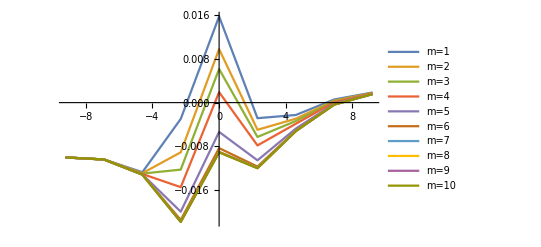

```mathematica
(******************************** Differences ***********************************)

(*  a log *)
alogdiff=Table[amatlog[[j]]-a[i][[j]],{i,10},{j,9}];
alogdiffset=Table[{logo[[j]],alogdiff[[i,j]]},{i,10},{j,9}];
ListLinePlot[Table[alogdiffset[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

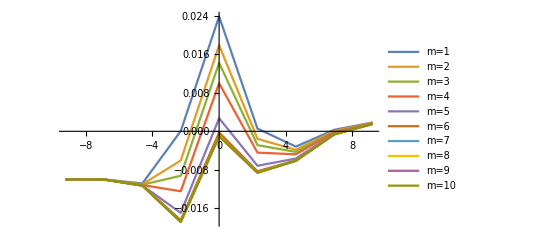

```mathematica
(*  a err *)
aerrdiff=Table[amaterr[[j]]-a[i][[j]],{i,10},{j,9}];
aerrdiffset=Table[{logo[[j]],aerrdiff[[i,j]]},{i,10},{j,9}];
ListLinePlot[Table[aerrdiffset[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

```mathematica
(* b exp *)
bdiff=Table[bmatexp[[j]]-b[i][[j]],{i,10},{j,9}];
bdiffset=Table[{logo[[j]],bdiff[[i,j]]},{i,10},{j,9}];
```

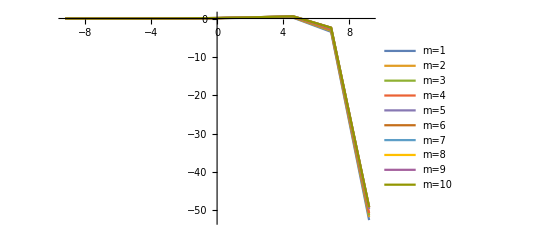

```mathematica
ListLinePlot[Table[bdiffset[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```